```mathematica
ClearAll["Global`*"]
```

Alignment of Lu^163 using the formalism from Chapter 4 of the PhdThesis

Exact formulas for the alignment:-Graphics-

Formula for the rotational frequency: -Graphics-

Fitting parameters

```mathematica
moiW1={63.2,20,10};
moiW1tsd4={67,34.5,50};
VW1=3.1;
VW1tsd4=0.7;
gmW1=17;
```

Experimental data (spins and excitation energies)

```mathematica
TSD1exp={{8.5,0.1966},{10.5,0.4597},{12.5,0.7746},{14.5,1.1609},{16.5,1.6112},{18.5,2.1265},{20.5,2.7051},{22.5,3.3441},{24.5,4.0411},{26.5,4.7937},{28.5,5.5992},{30.5,6.457},{32.5,7.3667},{34.5,8.3293},{36.5,9.3458},{38.5,10.4169},{40.5,11.5431},{42.5,12.7224},{44.5,13.9491},{46.5,15.2181},{48.5,16.5221}};
TSD2exp={{13.5,1.3394},{15.5,1.7467},{17.5,2.2184},{19.5,2.7527},{21.5,3.3484},{23.5,4.003},{25.5,4.7143},{27.5,5.4805},{29.5,6.3004},{31.5,7.1733},{33.5,8.0998},{35.5,9.08},{37.5,10.1147},{39.5,11.2036},{41.5,12.3466},{43.5,13.5441},{45.5,14.7911}};
TSD3exp={{16.5,2.1237},{18.5,2.6293},{20.5,3.1973},{22.5,3.8243},{24.5,4.5094},{26.5,5.2506},{28.5,6.0465},{30.5,6.8963},{32.5,7.7988},{34.5,8.7546},{36.5,9.7638},{38.5,10.8268},{40.5,11.9392},{42.5,13.0861}};
TSD4exp={{23.5,4.58},{25.5,5.2251},{27.5,5.9273},{29.5,6.6819},{31.5,7.4919},{33.5,8.3573},{35.5,9.2778},{37.5,10.2535},{39.5,11.2851},{41.5,12.3701}};
homega[e1_,e2_]:=(e1-e2)/2;
tsd1Exp=Table[TSD1exp[[i,2]],{i,1,Length[TSD1exp]}];
tsd2Exp=Table[TSD2exp[[i,2]],{i,1,Length[TSD2exp]}];
tsd3Exp=Table[TSD3exp[[i,2]],{i,1,Length[TSD3exp]}];
tsd4Exp=Table[TSD4exp[[i,2]],{i,1,Length[TSD4exp]}];
```

Theoretical data, obtained using the parameters given below:

```mathematica
spins1=Table[i,{i,17/2,97/2,2}];
spins2=Table[i,{i,27/2,91/2,2}];
spins3=Table[i,{i,33/2,85/2,2}];
spins4=Table[i,{i,47/2,83/2,2}];
```

```mathematica
tsd1Th={0.1782313339095538,0.4196718015490277,0.7243621940188483,1.0923154913463209,1.523534139749048,2.0180166923766896,2.575760521067923,3.196762935382364,3.8810216185253013,4.628534762745778,5.4393010737500855,6.313319721650804,7.250590274255138,8.25111262894795,9.314886950091982,10.441913614400999,11.632193164646008,12.885726271127783,14.202513699996903,15.582556287428215,17.02585491870882};
tsd2Th={0.9004306858462805,1.3000166888051228,1.7628675824531712,2.2889811210917306,2.8783545610814096,3.530985368705724,4.246871475498511,5.026011334403566,5.868403891106577,6.7740485232333025,7.742944971643716,8.775093274563535,9.870493708832292,11.029146739474438,12.251052977390533,13.536213144377303,14.884628044497596};
tsd3Th={1.8623070240633441,2.3814254518465225,2.9627336139117766,3.606268066904919,4.312065580008616,5.080163795237553,5.91060122612018,6.80341697938032,7.758650383962188,8.77634061569537,9.85652635810116,10.999245515511404,12.20453498222583,13.472430465206731};
tsd4Th={3.1866338682453352,3.8323362382052784,4.537678945748995,5.302667932987546,6.1273085414844655,7.01160554371423,7.955563190121492,8.959185261250264,10.022475119402822,11.145435757088617};
```

Harris parameters

```mathematica
h0=30;
h1=40;
Iref[omega_]:=h0*omega+h1*omega^3;
Ix[spin_,omega_]:=spin - Iref[omega];
```

```mathematica
omega1Exp=Table[homega[tsd1Exp[[i]],tsd1Exp[[i-1]]],{i,2,Length[tsd1Exp]}];
omega2Exp=Table[homega[tsd2Exp[[i]],tsd2Exp[[i-1]]],{i,2,Length[tsd2Exp]}];
omega3Exp=Table[homega[tsd3Exp[[i]],tsd3Exp[[i-1]]],{i,2,Length[tsd3Exp]}];
omega4Exp=Table[homega[tsd4Exp[[i]],tsd4Exp[[i-1]]],{i,2,Length[tsd4Exp]}];
omega1Th=Table[homega[tsd1Th[[i]],tsd1Th[[i-1]]],{i,2,Length[tsd1Th]}];
omega2Th=Table[homega[tsd2Th[[i]],tsd2Th[[i-1]]],{i,2,Length[tsd2Th]}];
omega3Th=Table[homega[tsd3Th[[i]],tsd3Th[[i-1]]],{i,2,Length[tsd3Th]}];
omega4Th=Table[homega[tsd4Th[[i]],tsd4Th[[i-1]]],{i,2,Length[tsd4Th]}];
```

```mathematica
align1Exp=Table[{omega1Exp[[i]],Ix[spins1[[i+1]],omega1Exp[[i]]]},{i,1,Length[omega1Exp]}];
align2Exp=Table[{omega2Exp[[i]],Ix[spins2[[i+1]],omega2Exp[[i]]]},{i,1,Length[omega2Exp]}];
align3Exp=Table[{omega3Exp[[i]],Ix[spins3[[i+1]],omega3Exp[[i]]]},{i,1,Length[omega3Exp]}];
align4Exp=Table[{omega4Exp[[i]],Ix[spins4[[i+1]],omega4Exp[[i]]]},{i,1,Length[omega4Exp]}];
align1Th=Table[{omega1Th[[i]],Ix[spins1[[i+1]],omega1Th[[i]]]},{i,1,Length[omega1Th]}];
align2Th=Table[{omega2Th[[i]],Ix[spins2[[i+1]],omega2Th[[i]]]},{i,1,Length[omega2Th]}];
align3Th=Table[{omega3Th[[i]],Ix[spins3[[i+1]],omega3Th[[i]]]},{i,1,Length[omega3Th]}];
align4Th=Table[{omega4Th[[i]],Ix[spins4[[i+1]],omega4Th[[i]]]},{i,1,Length[omega4Th]}];
```

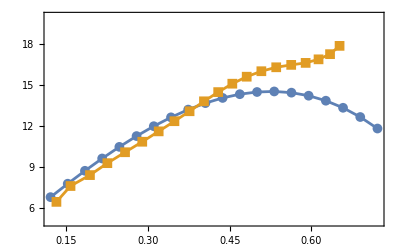

```mathematica
Show[ListPlot[{align1Th, align1Exp},Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False],PlotRange->{5,20}]
```

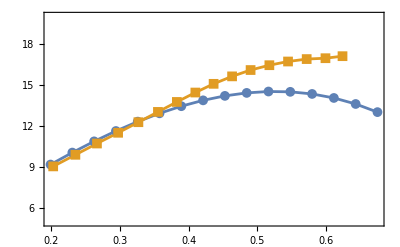

```mathematica
Show[ListPlot[{align2Th, align2Exp},Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False],PlotRange->{5,20}]
```

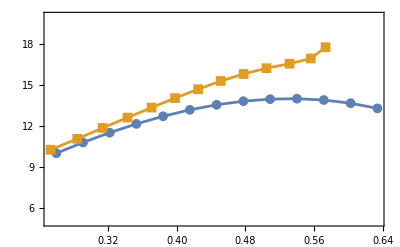

```mathematica
Show[ListPlot[{align3Th, align3Exp},Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False],PlotRange->{5,20}]
```

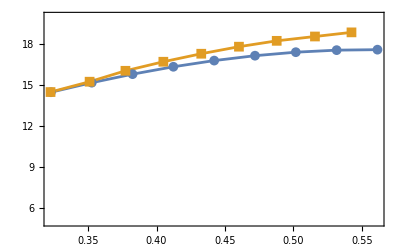

```mathematica
Show[ListPlot[{align4Th, align4Exp},Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False],PlotRange->{5,20}]
```